```mathematica
Quit
```

# Commuting, Migration, and Local Employment Elasticities

## by Ferdinando Monte, Stephen J. Redding and Esteban Rossi-Hansberg

American Economic Review, forthcoming 2018

This Mathematica notebook generates data for all the counterfactual simulations in the paper, with exclusion of the Commuting Zone-level calibration (see cmlee_CZ.nb) and the calibration with partially locally owned and partially nationally owned land (see cmlee_ED.nb).

The section “Setup, Import Data” sets up the simulation and loads external data.

The section “Functions” compiles routines to be used in the subsequent analysis.

The section “Data Preparation” computes productivities, county-level trade deficits, and exports data for reduced form analysis (such as partial equilibrium elasticities and county productivities).

The section “Counterfactual Simulations” performs the exercises in the paper and web appendix.

## Setup, Import Data

### Setup

Setting history length to zero to avoid large memory usage during iterations

```mathematica
$HistoryLength=0;
SetDirectory["C:\\Users\\Samuel Zhao\\OneDrive\\Documents\\CMLEE"];
```

### Importing county data

This section imports data about initial equilibrium variables at county level.

```mathematica
(*Workplace data*)
workplaceEmp=Flatten[Import["simulation inputs\\workplaceEmp.csv"]]; (*number of jobs*)
workplaceWage=Flatten[Import["simulation inputs\\workplaceWage.csv"]];(*average yearly wage of a job by workplace, dollars*)
laborIncome=(workplaceEmp workplaceWage)/10^6; (*total payment to workers in a workplace, in millions*)

(*Residence data*)
resWage=Flatten[Import["simulation inputs\\residentialWage.csv"]];(*average yearly wage of a job by residence, dollars*)
resEmp=Flatten[Import["simulation inputs\\residentialEmp.csv"]];(*number of residents in a residential location*)
resIncome=Flatten[Import["simulation inputs\\resIncome.csv"]]; (*total residential income, millions*)

(*bilateral distances*) 
distancesOnlyTrading=Import["simulation inputs\\distances_onlytrading.csv"]; (* when two counties do not trade, distance is 10^9; a row is an origin county, selling to all destination-columns counties (see below as well) *)
distancesAllPairs=Import["simulation inputs\\distances_allpairs.csv"]; (*distances when all counties are allowed to trade - all bilateral distances*)

(*commuters residing in a row location and working in a column location*)
λ=Import["simulation inputs\\commuting_flows.csv"];  

(*land area*)
landArea=Flatten[Import["simulation inputs\\land_area.csv"]];

(*other*)
countyNames=Import["simulation inputs\\county_names.csv"]; 
ncounties=Length[workplaceEmp];
mfgShares=Flatten[Import["simulation inputs\\mfg_shares.csv"]];
```

```mathematica
(*saiz implied population elasticities*) 
ηzero=Table[0.,{i,1,ncounties}]; (*baseline model elasticity*) 
ηexf=Flatten[Import["simulation inputs\\saiz_price_elasticities.csv"]]; (*elasticities for main exercise with positive land supply*)
```

### Importing other data

Correspondence between counties and cfs area. It is used in recovering the bilateral productivity estimates. 
The first column is a CFS identifier, the second is a county identifier (different from the fips code) from 1 to 3,111. Counties are always ordered by fips code, so the first row (or the first column) in the costMeasure and shares data is county number 1 in this data.

```mathematica
beaCfs=Import["simulation inputs\\bea_cfs_list.csv"];
Dimensions[beaCfs]
beaCfs[[1;;4]]
```

{3111,2}

{{3,1},{2,2},{3,3},{1,4}}

### Parameters

```mathematica
σ=4;
ψ=-1.2922/(1-σ);(*this ψ(1-σ) comes from the estimated gravity coefficient on CFS-level regressions*)
α=0.6;
ϵ=3.3035;
ϕ =4.4295/ϵ;
```

### Fixed variable values

These variables are used in the counterfactual exercises (compiled function and the iteration modules), and never change across simulations.

Matrix with indicators for whether a pair is a commuting possibility; the matrix with commuting flows (persons rather than shares) is λ:

```mathematica
isCommuting=Table[If[λ[[i,j]]==0,0,1],{i,1,ncounties},{j,1,ncounties}];
isCommutingSp=SparseArray[isCommuting];
isNoCommuting=DiagonalMatrix[Table[1,{i,1,ncounties}]];
isNoCommutingSp=SparseArray[isNoCommuting];
```

Total population (number of jobs)

```mathematica
population=Total[workplaceEmp];
```

## Functions

Productivity Estimates

Compiled function to compute new guess of labor income on a local labor market (this is the RHS of the iteration below, productivities)

```mathematica
rhsProductivities=Compile[{{prod,_Real,1},{num,_Real,2},{expenditure,_Real,1}},
Module[{bilatRes,multResistance,effDemand,leh},
bilatRes=num prod;(*proportional to bilateral cost*)
multResistance=Total[bilatRes]; (*denominator in RHS*)
effDemand=expenditure/multResistance; (*income/denominator in RHS*)
leh= bilatRes.effDemand; 
leh
](*RHS with current guess of productivity*)
];
```

Loop to compute productivities. This function receives 1) workplace employment (in persons), 2) workplace wage per person (in dollars), 3) total residential expenditure (in millions) and 4) a bilateral distance matrix (all pairs, or only county trading in the cfs data); residential expenditure allows for deficits.
It returns productivity levels that exactly rationalize the data on workplace income and residential expenditure. It uses the rhsProductivities function above to compute new rhs during the iterations.

```mathematica
productivities[workemp_,workwage_,resExp_,distmatrix_,detailsYN_]:=Module[{A0,λ,tol,c,dist,distmin,gap,labIncomeHat,A1,den,numerators,labIncome},
λ=0.7; (*step size *)
A0=Table[1.,{i,1,ncounties}]; (*initial condition for productivities*)

tol=10^-6; (*tolerance level*)
c=0;
dist=1;
numerators=(workemp (workwage/10^4)^(1-σ) ) (distmatrix)^(ψ(1-σ)); 
labIncome=(workemp workwage)/10^6; (*left hand side of trade flows equation*)

(*Note that the iterations solve for A^(σ-1); before returning the output, these guesses are rescaled to the 1/(σ-1).*)
While[dist>tol &&  c<10000,
c=c+1;

(*New labor Expenditure*)
labIncomeHat=rhsProductivities[A0,numerators,resExp];


 (*Relative gap in labor expenditure*)
gap=labIncome /labIncomeHat;
dist=Max[Abs[gap-1]];
distmin=Min[Abs[gap-1]];

 (*new guess of productivity*)
A1=(λ + (1-λ)gap)A0; 
den=Mean[A1];
A0=A1/den;

(*diagnostics*)
If[Mod[c,50]==1  && dist>0.01 && detailsYN==1,
Block[{},
Print["end of iteration ",c, " at " DateString[], "; min gap: ", distmin,"; max gap: ",dist,  " - ",Min[A0]," ",Max[A0]];
];
];
];
If[detailsYN==1,Block[{},
Print["end of iteration ",c, " at " DateString[], "; max gap: ",dist, " ",Min[A0]," ",Max[A0]];
]];
A0=A0^(1/(σ-1))/Mean[A0^(1/(σ-1))]; (*Recovering productivities from the A^(σ-1) values that fit the data*)
A0
];
```

Trade

Function to compute trade flows and trade shares given productivities, workplace employment and wage, residential expenditure, distance matrix.
The function returns 1) a matrix of trade shares - for each row origin, the shares of expenditure of each destination' s income on it, and 2) the corresponding trade flow values in millions of dollars.

```mathematica
trade=Compile[{{prod,_Real,1},{workemp,_Real,1},{workwage,_Real,1},{expenditure,_Real,1},{distmatrix,_Real,2}},
Module[{num,bilatRes,multResistance,share,trade},
num=(workemp (workwage/10^4)^(1-σ) ) (distmatrix)^(ψ(1-σ));
bilatRes=num prod^(σ-1);(*proportional to bilateral cost*)
multResistance=Total[bilatRes]; (*denominator in RHS*)
share=Transpose[Transpose[bilatRes]/multResistance ];
trade=Transpose[Transpose[share] expenditure];
{share,trade}
](*RHS with current guess of productivity*)
];
```

Counterfactual simulations

## Changes in any parameter

#### Guess Update

This compiled function appears in iterations: it takes as input a current what and λhat proposals - given trade and commuting costs - and gives back new proposals.

```mathematica
allChangesGuess=Compile[{{inWhat,_Real,1},{inλ,_Real,2},{khat,_Real,2},{dhat,_Real,2},{ahat,_Real,1},{bhat,_Real,2},{χ,_Real,1}},

allChangesGuessMod=Module[{iterVbar,iterLM,iterLR,iterQ,iterπni,iterP,iterλtilde,iterWtilde,distWages,distλ,wout,λout,diag,
temp1,temp2,temp3,temp4,temp5,temp6,denRes,numRes,den,num,den2,temp7,temp8,outcome},

(*vbar hat*)
temp1=  (λ bhat)/khat^ϵ;
denRes=temp1.inWhat^ϵ;
numRes=temp1.(inWhat^(ϵ+1) workplaceWage);
iterVbar=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ inλ;
iterLM=Total[temp1]/workplaceEmp;
iterLR=Total[Transpose[temp1]]/resEmp;


(*q hat*)

iterQ=((resIncome iterVbar iterLR+deficit)/(resIncome+deficit) )^(1/(1+χ));  

(*πni hat*)
temp1=πniOnlyTrading dhat^(1-σ);
temp2=iterLM (inWhat/ahat)^(1-σ);
den=temp2.temp1; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=dhat^(1-σ) temp2;
iterπni=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[iterπni[[i,i]],{i,1,ncounties}];
iterP=inWhat/ahat(iterLM/diag)^(1/(1-σ))  ;

(*w hat, next iteration*)
temp1=πniOnlyTrading iterπni;
 
temp4=iterVbar iterLR  resIncome+deficit;
iterWtilde=(temp1.temp4)/(laborIncome iterLM);
iterWtilde=iterWtilde/Mean[iterWtilde];


(*λ hat, next iteration*)
temp7=iterP^-α iterQ^(-1+α);
temp6=bhat (Outer[Times,temp7,inWhat])^ϵ/khat^ϵ;
den2=Total[Total[λ temp6]];
iterλtilde=(temp6 population)/den2 ; (*to limit accumulation of numerical errors - unconditional shares of commuting 
have a very small order of magnitude - we predict new commuting flows in # of jobs; hence, the numerator is multiplied by the population level before dividing it for the sum
of all terms at the denominator; note that the denominator contains λ, which is in fact flows of jobs, rather than shares*)

(*output: matrix with ncounties+1 rows, and ncounties columns (iterWtilde is added as a last row)*)
outcome=Join[iterλtilde,{iterWtilde}];
outcome

]
];
```

#### Iterations ( hatChanges[khat, dhat, ahat, bhat, landel,outputEvery] )

This function iterates over what and λhat until convergence, and gives the equilibrium counterfactual changes. It takes in exogenous changes in commuting and trade costs. The last argument indicates every how many iterations we want output on the iteration progress (set 0 for no output at all during iterations; set -1 for no output at all).

```mathematica
hatChanges[khat_,dhat_,ahat_,bhat_,landel_,outputEvery_]:=Module[{dist,c,what,λhat,inWhat,inλ,out,iterλtilde,iterWtilde,distWages,distλ,
temp1,denRes,numRes,Vbarhat,LMhat,LRhat,Qhat,temp2,den,num,πnihat,diag,Phat,pricehat,realinchat},
dist=1;
c=0;
what=Table[1,{i,1,ncounties}];
λhat=isCommuting;

While[c<maxiter && dist>tol,

c=c+1;
inWhat=what;
inλ=λhat;

out=allChangesGuess[inWhat,inλ,khat,dhat,ahat,bhat,landel];

iterλtilde=out[[1;;ncounties,All]] isCommutingSp;
iterWtilde=out[[ncounties+1,All]];

distWages=Max[Abs[iterWtilde/inWhat-1]];

(*using the sparse-array version of commuting allows saving time*)
distλ=Max[Abs[iterλtilde/(inλ+isCommutingSp-1) -1] isCommutingSp];
(*the denominator makes sure that the division by zero never occurs, while preserving the deviations for observed commuting pairs; then, the matrix is multiplied by commuting indicators to restore zero change where there are no commuting flows*)
what=inWhat ζ + iterWtilde (1-ζ);
λhat=inλ  ζ + iterλtilde (1-ζ);

dist=Max[{distWages,distλ}];

If[outputEvery>0 &&Mod[c,outputEvery]==1, Print["Iteration ",c,"  concluded on ",DateString[], "; distWages is ",distWages,"; distλ is ",distλ,"."]];
];
If[dist>tol,
Print["WARNING: Max iterations reached witout satisfying the required tolerance. Current sup-norm distances: distWages: ",distWages,"; distλ: ",distλ," ..."],
If[outputEvery>-1,
Print["Convergence achieved in ",c," iterations on ",DateString[],"; distWages is ",distWages,"; distλ is ",distλ," ..."]
]];

(*Computing equilibrium changes*)

(*vbar hat*)
temp1= (bhat λ)/khat^ϵ ; 
denRes=temp1.what^ϵ;
numRes=temp1.(what^(ϵ+1) workplaceWage);
Vbarhat=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ λhat;
LMhat=Total[temp1]/workplaceEmp;
LRhat=Total[Transpose[temp1]]/resEmp;


(*q hat*)

Qhat=((resIncome Vbarhat LRhat+deficit)/(resIncome+deficit))^(1/(1+landel)); 


(*πni hat*)
temp1=πniOnlyTrading dhat^(1-σ);
temp2=LMhat (what/ahat)^(1-σ);
den=temp2.temp1; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=dhat^(1-σ) temp2;
πnihat=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[πnihat[[i,i]],{i,1,ncounties}];
Phat=what/ahat(LMhat/diag)^(1/(1-σ))  ; 

(*price index hat*)
pricehat=Phat^α Qhat^(1-α);

(*real income of residents*)
realinchat=Vbarhat/pricehat; 


If[outputEvery>-1,Print["Counterfactuals completed on ",DateString[],"."]];

{what,Vbarhat,realinchat,LMhat,LRhat,Qhat,Phat,pricehat,λhat,πnihat,c,distWages,distλ}

];
```

## Changes in any parameter, arbitrary initial conditions

#### Guess update

This compiled function appears in iterations: it takes as input a current what and λhat proposals - given trade and commuting costs - and gives back new proposals.

```mathematica
allChangesArbGuess=Compile[{{inWhat,_Real,1},{inλ,_Real,2},{khat,_Real,2},{dhat,_Real,2},{ahat,_Real,1},{bhat,_Real,2},
{λArb,_Real,2},{workplaceWageArb,_Real,1},{resWageArb,_Real,1},{workplaceEmpArb,_Real,1},{resEmpArb,_Real,1},{tradeSharesArb,_Real,2},{resIncomeArb,_Real,1},{workIncomeArb,_Real,1},{χ,_Real,1}},

allChangesArbGuessMod=Module[{iterVbar,iterLM,iterLR,iterQ,iterπni,iterP,iterλtilde,iterWtilde,distWages,distλ,wout,λout,diag,
temp1,temp2,temp3,temp4,temp5,temp6,denRes,numRes,den,num,den2,temp7,temp8,outcome},

(*vbar hat*)
temp1=  (λArb bhat)/khat^ϵ;
denRes=temp1.inWhat^ϵ;
numRes=temp1.(inWhat^(ϵ+1) workplaceWageArb);
iterVbar=numRes/(resWageArb  denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λArb inλ;
iterLM=Total[temp1]/workplaceEmpArb;
iterLR=Total[Transpose[temp1]]/resEmpArb;


(*q hat*)

iterQ=((resIncomeArb iterVbar iterLR+deficit)/(resIncomeArb+deficit))^(1/(1+χ)); 

(*πni hat*)
temp1=tradeSharesArb dhat^(1-σ);
temp2=iterLM (inWhat/ahat)^(1-σ);
den=temp2.temp1; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=dhat^(1-σ) temp2;
iterπni=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[iterπni[[i,i]],{i,1,ncounties}];
iterP=inWhat/ahat(iterLM/diag)^(1/(1-σ))  ;

(*w hat, next iteration*)
temp1=tradeSharesArb iterπni;

temp4=resIncomeArb iterVbar iterLR+deficit;
iterWtilde=(temp1.temp4)/(workIncomeArb  iterLM);
iterWtilde=iterWtilde/Mean[iterWtilde];


(*λ hat, next iteration*)
temp7=iterP^-α iterQ^(-1+α);
temp6=bhat (Outer[Times,temp7,inWhat])^ϵ/khat^ϵ;
den2=Total[Total[λArb temp6]];
iterλtilde=(temp6 population)/den2 ;  (*to limit accumulation of numerical errors - unconditional shares of commuting 
have a very small order of magnitude - we predict new commuting flows in # of jobs; hence, the numerator is multiplied by the population level before dividing it for the sum
of all terms at the denominator; note that the denominator contains λ, which is in fact flows of jobs, rather than shares*)

(*output*)
outcome=Join[iterλtilde,{iterWtilde}];
outcome

]
];
```

#### Iterations ( hatChangesArb[khat, dhat ,ahat ,bhat, λArb, workplaceWageArb, resWageArb, workplaceEmpArb, resEmpArb, tradeSharesArb, resIncomeArb, workIncomeArb, landel,outputEvery] )

This function iterates over what and λhat until convergence, and gives the equilibrium counterfactual changes. It takes in exogenous changes in commuting and trade costs. The third argument indicates every how many iterations we want output on the iteration progress (set 0 for no output at all).

```mathematica
hatChangesArb[khat_,dhat_,ahat_,bhat_,
λArb_,workplaceWageArb_,resWageArb_,workplaceEmpArb_,resEmpArb_,tradeSharesArb_,resIncomeArb_,workIncomeArb_,landel_,
outputEvery_]:=Module[

{dist,c,what,λhat,inWhat,inλ,out,iterλtilde,iterWtilde,distWages,distλ,
temp1,denRes,numRes,Vbarhat,LMhat,LRhat,Qhat,temp2,den,num,πnihat,diag,Phat,pricehat,realinchat},
dist=1;
c=0;
what=Table[1,{i,1,ncounties}];
λhat=isCommuting;

While[c<maxiter && dist>tol,

c=c+1;
inWhat=what;
inλ=λhat;

out=allChangesArbGuess[inWhat,inλ,khat,dhat,ahat,bhat,λArb,workplaceWageArb,resWageArb,workplaceEmpArb,resEmpArb,tradeSharesArb,resIncomeArb,workIncomeArb,landel];


iterλtilde=out[[1;;ncounties,All]] isCommutingSp;
iterWtilde=out[[ncounties+1,All]];

distWages=Max[Abs[iterWtilde/inWhat-1]];

(*using the sparse-array version of commuting allows saving time*)
distλ=Max[Abs[iterλtilde/(inλ+isCommutingSp-1) -1] isCommutingSp];
(*the denominator makes sure that the division by zero never occurs, while preserving the deviations for observed commuting pairs; then, the matrix is multiplied by commuting indicators to restore zero change where there are no commuting flows*)
what=inWhat ζ + iterWtilde (1-ζ);
λhat=inλ  ζ + iterλtilde (1-ζ);

dist=Max[{distWages,distλ}];

If[outputEvery>0 &&Mod[c,outputEvery]==1, Print["Iteration ",c,"  concluded on ",DateString[], "; distWages is ",distWages,"; distλ is ",distλ,"."]];
];
If[dist>tol,
Print["WARNING: Max iterations reached without satisfying the required tolerance. Current sup-norm distances: distWages: ",distWages,"; distλ: ",distλ," ..."],
If[outputEvery>-1,
Print["Convergence achieved in ",c," iterations on ",DateString[],"; distWages is ",distWages,"; distλ is ",distλ," ..."]
]];

(*Computing equilibrium changes*)

(*vbar hat*)
temp1= (bhat λArb)/khat^ϵ  ;  
denRes=temp1.what^ϵ;
numRes=temp1.(what^(ϵ+1) workplaceWageArb);
Vbarhat=numRes/(resWageArb  denRes); 


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λArb λhat;
LMhat=Total[temp1]/workplaceEmpArb; 
LRhat=Total[Transpose[temp1]]/resEmpArb; 


(*q hat*)

Qhat=((resIncomeArb Vbarhat LRhat+deficit)/(resIncomeArb+deficit))^(1/(1+landel)); 

(*πni hat*)
temp1=tradeSharesArb dhat^(1-σ);
temp2=LMhat (what/ahat)^(1-σ);
den=temp2.temp1; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=dhat^(1-σ) temp2;
πnihat=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[πnihat[[i,i]],{i,1,ncounties}];
Phat=what/ahat(LMhat/diag)^(1/(1-σ))  ; 

(*price index hat*)
pricehat=Phat^α Qhat^(1-α);

(*real income of residents*)
realinchat=Vbarhat/pricehat; 


If[outputEvery>-1,Print["Counterfactuals completed on ",DateString[],"."]];

{what,Vbarhat,realinchat,LMhat,LRhat,Qhat,Phat,pricehat,λhat,πnihat,c,distWages,distλ}

];
```

## Only changes in productivity

#### Guess Update

```mathematica
prodChangesGuess=Compile[{{inWhat,_Real,1},{inλ,_Real,2},{ahat,_Real,1},{ones,_Real,1},{χ,_Real,1}},

prodChangesGuessMod=Module[{iterVbar,iterLM,iterLR,iterQ,iterπni,iterP,iterλtilde,iterWtilde,distWages,distλ,wout,λout,diag,
temp1,temp2,temp3,temp4,temp5,temp6,denRes,numRes,den,num,den2,temp7,temp8,outcome},

(*vbar hat*)
denRes=λ.inWhat^ϵ;
numRes=λ.(inWhat^(ϵ+1) workplaceWage);
iterVbar=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ inλ;
iterLM=Total[temp1]/workplaceEmp;
iterLR=Total[Transpose[temp1]]/resEmp;


(*q hat*)

iterQ=((resIncome iterVbar iterLR+deficit)/(resIncome+deficit) )^(1/(1+χ));

(*πni hat*)
temp2=iterLM (inWhat/ahat)^(1-σ);
den=temp2.πniOnlyTrading; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=Outer[Times,temp2,ones];
iterπni=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[iterπni[[i,i]],{i,1,ncounties}];
iterP=inWhat/ahat(iterLM/diag)^(1/(1-σ))  ;

(*w hat, next iteration*)
temp1=πniOnlyTrading iterπni;

temp4=iterVbar iterLR  resIncome+deficit;
iterWtilde=(temp1.temp4)/(laborIncome iterLM);
iterWtilde=iterWtilde/Mean[iterWtilde];


(*λ hat, next iteration*)
temp7=iterP^-α iterQ^(-1+α);
temp6=(Outer[Times,temp7,inWhat])^ϵ;
den2=Total[Total[λ temp6]];
iterλtilde=(temp6 population)/den2 ;  (*to limit accumulation of numerical errors - unconditional shares of commuting 
have a very small order of magnitude - we predict new commuting flows in # of jobs; hence, the numerator is multiplied by the population level before dividing it for the sum
of all terms at the denominator; note that the denominator contains λ, which is in fact flows of jobs, rather than shares*)

(*output*)
outcome=Join[iterλtilde,{iterWtilde}];
outcome

]
];
```

#### Iterations ( hatChangesA[ahat,landel, outputEvery] )

```mathematica
hatChangesA[ahat_,landel_,outputEvery_]:=Module[{dist,c,what,λhat,inWhat,inλ,out,iterλtilde,iterWtilde,distWages,distλ,ones,
temp1,denRes,numRes,Vbarhat,LMhat,LRhat,Qhat,temp2,den,num,πnihat,diag,Phat,pricehat,realinchat},
dist=1;
c=0;
what=Table[1,{i,1,ncounties}];
λhat=isCommuting;
ones=Table[1,{i,1,ncounties}];

While[c<maxiter && dist>tol,

c=c+1;
inWhat=what;
inλ=λhat;

out=prodChangesGuess[inWhat,inλ,ahat,ones,landel];

iterλtilde=out[[1;;ncounties,All]] isCommutingSp;
iterWtilde=out[[ncounties+1,All]];

distWages=Max[Abs[iterWtilde/inWhat-1]];

(*using the sparse-array version of commuting allows saving time*)
distλ=Max[Abs[iterλtilde/(inλ+isCommutingSp-1) -1] isCommutingSp];
(*the denominator makes sure that the division by zero never occurs, while preserving the deviations for observed commuting pairs; then, the matrix is multiplied by commuting indicators to restore zero change where there are no commuting flows*)
what=inWhat ζ + iterWtilde (1-ζ);
λhat=inλ  ζ + iterλtilde (1-ζ);

dist=Max[{distWages,distλ}];

If[outputEvery>0 &&Mod[c,outputEvery]==1, Print["Iteration ",c,"  concluded on ",DateString[], "; distWages is ",distWages,"; distλ is ",distλ,"."]];
];
If[dist>tol,
Print["WARNING: Max iterations reached witout satisfying the required tolerance. Current sup-norm distances: distWages: ",distWages,"; distλ: ",distλ," ..."],
If[outputEvery>-1,
Print["Convergence achieved in ",c," iterations on ",DateString[],"; distWages is ",distWages,"; distλ is ",distλ," ..."]
]];

(*Computing equilibrium changes*)

(*vbar hat*)
denRes=λ.what^ϵ;
numRes=λ.(what^(ϵ+1) workplaceWage);
Vbarhat=numRes/(resWage denRes);


(*lm hat and lr hat*)
(*note: λ are already flows, i.e. shares times Lbar in the equations*)
temp1=λ λhat;
LMhat=Total[temp1]/workplaceEmp;
LRhat=Total[Transpose[temp1]]/resEmp;


(*q hat*)

Qhat=((resIncome Vbarhat LRhat+deficit)/(resIncome+deficit) )^(1/(1+landel));  

(*πni hat*)
temp2=LMhat (what/ahat)^(1-σ);
den=temp2.πniOnlyTrading; (*note that left-product effectively gives the transpose of temp1 times temp2.*)
num=Outer[Times, temp2,ones];
πnihat=Transpose[Transpose[num]/den  ] ;(*the term inside divides each column by the correspondent element of the denominator; it then brings the matrix in the original form*)


(*P hat*)
diag=Table[πnihat[[i,i]],{i,1,ncounties}];
Phat=what/ahat(LMhat/diag)^(1/(1-σ))  ; 

(*price index hat*)
pricehat=Phat^α Qhat^(1-α);

(*real income of residents*)
realinchat=Vbarhat/pricehat; 


If[outputEvery>-1,Print["Counterfactuals completed on ",DateString[],"."]];


{what,Vbarhat,realinchat,LMhat,LRhat,Qhat,Phat,pricehat,λhat,πnihat,c,distWages,distλ}

];
```

Other functions

## Productivity shocks to a set of counties

This function is used to simulate productivity shocks to one county (or a set of counties) inside a loop. It saves outcomes for all the economy with a given set of shocks, plus statistics on convergence used to check that all iterations concluded correctly.
It is used in 5% productivity shocks to counties and commuting zones, for example.

```mathematica
countyProdShock[rep_,prodChange_,landel_]:=Module[
{outcome,out,filename,caseN,repN,dataOutTreat,dataOutControl,measuredProdhat,shipmentsHat,allData,treatment,countyline,
whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,πnnhat,c,distWages,distλ,replication},





(*computing outcome*)
outcome=hatChangesA[prodChange,landel,-1];

(*ALL COUNTIES OUTCOMES*)
	(*storing all counties outcome*)
	{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=outcome-1;
	{c,distWages,distλ}={c,distWages,distλ}+1;

	λhatOut=Diagonal[λhatOut]; (*own commuting change*)
	πnihatOut=Diagonal[πnihatOut];(*own trade share change*)
	measuredProdhat=((LMhatOut+1)/(πnihatOut+1))^(1/(σ-1))prodChange-1;(*measured productivity from cpi index*)
	shipmentsHat=(LMhatOut+1)(whatOut+1)-1;
	countyline=Table[i,{i,1,ncounties}];
	replication=Table[rep,{i,1,ncounties}];
	(*data to export*)
	allData={replication,countyline,whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,prodChange-1,measuredProdhat,shipmentsHat};

	Clear[out];
	out=Join[varnames,allData,2];
	out=Transpose[out];
	out=Join[countyNames,out,2];

	
	
Print[" Replication ", rep, " concluded at ",DateString[]];
(*the third column is 1 for treatment, 0 for control outcome*)
{out,c,distWages,distλ}

];
```

## Productivity shocks to a set of counties, with arbitrary initial conditions

```mathematica
countyProdShockArb[rep_,khat_, dhat_ ,prodChange_ ,bhat_, λArb_, workplaceWageArb_, resWageArb_, workplaceEmpArb_, resEmpArb_, tradeSharesArb_, resIncomeArb_, workIncomeArb_, landel_]:=Module[
{outcome,out,filename,caseN,repN,dataOutTreat,dataOutControl,measuredProdhat,shipmentsHat,allData,treatment,countyline,
whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,πnnhat,c,distWages,distλ,replication},




(*computing outcome*)
outcome=hatChangesArb[khat, dhat ,prodChange ,bhat, λArb, workplaceWageArb, resWageArb, workplaceEmpArb, resEmpArb, tradeSharesArb, resIncomeArb, workIncomeArb, landel, -1];

(*ALL COUNTIES OUTCOMES*)
	(*storing all counties outcome*)
	{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=outcome-1;
	{c,distWages,distλ}={c,distWages,distλ}+1;

	λhatOut=Diagonal[λhatOut]; (*own commuting change*)
	πnihatOut=Diagonal[πnihatOut];(*own trade share change*)
	measuredProdhat=((LMhatOut+1)/(πnihatOut+1))^(1/(σ-1))prodChange-1;(*measured productivity from cpi index*)
	shipmentsHat=(LMhatOut+1)(whatOut+1)-1;
	countyline=Table[i,{i,1,ncounties}];
	replication=Table[rep,{i,1,ncounties}];
	(*data to export*)
	allData={replication,countyline,whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,prodChange-1,measuredProdhat,shipmentsHat};

	Clear[out];
	out=Join[varnames,allData,2];
	out=Transpose[out];
	out=Join[countyNames,out,2];

	
	
Print[" Replication ", rep, " concluded at ",DateString[]];
(*the third column is 1 for treatment, 0 for control outcome*)
{out,c,distWages,distλ}

];
```

## Data Preparation

Productivities and Associated Trade Flows

## Assigning deficits

### Importing CFS data

The n-th row in the beaCfs data (n=1 to 3111) has two elements: the CFS number F and the county number C. Here I generate a list of 123 elements; the k-th element contains the list of counties belonging to the k-th CFS area: the set of instructions in the “table” command below say: 1) “assign the county number C (in the second element) to the list number F (in the first element); 2) record in which position in this list the county C is placed (the first, the second.... in the corresponding CFS); this index is necessary to go back from the beaCfs correspondence to the beaCfs file.

```mathematica
beaCfsCorr=Table[{},{i,1,123}];
beaCfsIndex={};
Table[Block[{},
beaCfsCorr[[ beaCfs[[n,1]] ]]=Join[beaCfsCorr[[ beaCfs[[n,1]] ]],{beaCfs[[n,2]]}];
beaCfsIndex=Join[beaCfsIndex,{Length[beaCfsCorr[[ beaCfs[[n,1]] ]]]}];
],{n,1,ncounties}];
```

```mathematica
Total[Table[Length[beaCfsCorr[[i]]],{i,1,123}]]
```

3111

Importing CFS trade data: sales from a CFS origin (row) to any CFS destination (column)

```mathematica
cfsData=Import["simulation inputs\\bilateral_cfs_trade.csv"];
Dimensions[cfsData]
```

{123,123}

Statistics on CFS deficits as a share of expenditure;

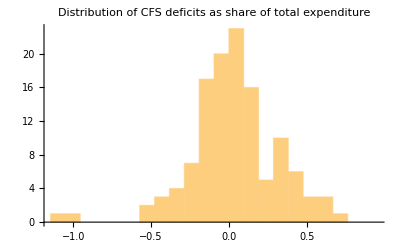

Mean: 0.033; Min: -1.145; Max: 0.952

quantile | CFS deficit
0.01 | -0.984
0.05 | -0.395
0.1 | -0.275
0.5 | 0.019
0.9 | 0.395
0.95 | 0.478
0.99 | 0.737

```mathematica
defExpenditure=(Total[cfsData]-Total[cfsData,{2}])/Total[cfsData];
Histogram[defExpenditure,{Min[defExpenditure],Quantile[defExpenditure,0.999],Quantile[defExpenditure,0.999]/10},
PlotLabel->"Distribution of CFS deficits as share of total expenditure"]
Print["Mean: ",Round[Mean[defExpenditure],0.001],"; Min: ",Round[Min[defExpenditure],0.001],"; Max: ",Round[Max[defExpenditure],0.001]];
Join[{{"quantile","CFS deficit"}},Table[{q,Quantile[Round[defExpenditure,0.001],q]},{q,{0.01,0.05,0.10,0.50,0.90,0.95,0.99}}]]//TableForm
```

### CFS trade deficits and allocation to counties

To allow for county level trade deficits, we compute the deficit at CFS level and then we impute this deficit at county-level in proportion to the residential income of each county. In general, it is not guaranteed that total expenditure is always positive for locations which are running a surplus. Hence, we rescale the CFS trade flows to match labor payments.

Creating a vector of labor payments to CFS workers (and checking they sum up to the total labor payment in the economy)

```mathematica
cfsLabExp=Table[{},{i,1,123}];
Table[cfsLabExp[[k]]=Table[laborIncome[[j]],{j,beaCfsCorr[[k]]}],{k,1,123}];
cfsLabExp=Total[cfsLabExp,{2}];
Total[cfsLabExp]-Total[laborIncome]
```

1.86265×10^-9

Creating a rescaled CFS trade matrix, where 1) total sales of any (row) origin match up to these cfs labor expenditure, keeping the destination composition of each origin fixed. The rationale is that total sales of a CFS, in a labor-only world, match to total labor payments to workers in the CFS (irrespective of their residence). We create a trade structure that matches the destination composition and the level of labor payments.

```mathematica
rescaledCfs=cfsData/Total[cfsData,{2}]  cfsLabExp;
```

The sum across rows of a given column gives a bea-consistent measure of expenditure of the CFS; hence, we can compute the cfs deficit as

```mathematica
cfsDeficit=Total[rescaledCfs]-Total[rescaledCfs,{2}];
```

This deficit is allocated across all counties that belong to the same CFS in proportion to their residential income. 
The table cfsResIncome contains for each CFS, a list of the residential incomes of all the counties; the table Increments contains, for each cfs k, a list of the addition to the residential income of all the counties in that cfs, as implied by the CFS deficit.

```mathematica
cfsResIncome=Table[{},{i,1,123}];
Table[cfsResIncome[[k]]=Table[resIncome[[j]],{j,beaCfsCorr[[k]]}],{k,1,123}];
increments=Table[cfsResIncome[[k]]/Total[cfsResIncome[[k]]] cfsDeficit[[k]],{k,1,123}];
resExpenditure=resIncome;
Table[resExpenditure[[i]]=resExpenditure[[i]]+ increments[[ beaCfs[[i,1]],beaCfsIndex[[i]] ]],{i,1,ncounties}];
```

Statistics on county-level deficits, as a share of county residential income

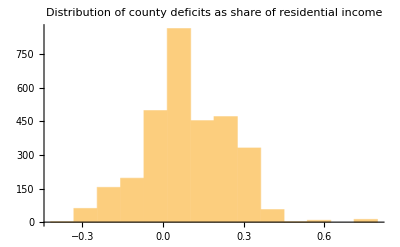

Mean: 0.092; Min: -0.418; Max: 7.1

quantile | county deficit
0.01 | -0.273
0.05 | -0.223
0.1 | -0.098
0.5 | 0.076
0.9 | 0.28
0.95 | 0.282
0.99 | 0.368

```mathematica
countyDeficit=resExpenditure/resIncome-1;

Histogram[countyDeficit,{Min[countyDeficit],Quantile[countyDeficit,0.999],Quantile[countyDeficit,0.999]/10},
PlotLabel->"Distribution of county deficits as share of residential income"]
Print["Mean: ",Round[Mean[countyDeficit],0.001],"; Min: ",Round[Min[countyDeficit],0.001],"; Max: ",Round[Max[countyDeficit],0.001]];
Join[{{"quantile","county deficit"}},Table[{q,Quantile[Round[countyDeficit,0.001],q]},{q,{0.01,0.05,0.10,0.50,0.90,0.95,0.99}}]]//TableForm
```

Comparing the distributions of deficits at cfs and county level

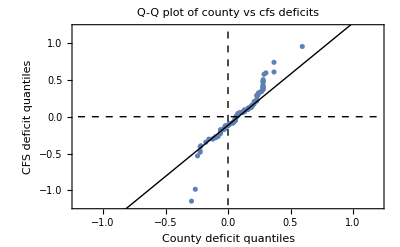

```mathematica
Show[
QuantilePlot[defExpenditure,countyDeficit,ReferenceLineStyle->Red,
FrameLabel->{"County deficit quantiles","CFS deficit quantiles"},PlotLabel->"Q-Q plot of county vs cfs deficits",PlotRange->{{-1.2,1.2},{-1.2,1.2}}],
ParametricPlot[{{0,x},{x,0}},{x,-1.2,1.2},PlotStyle->Directive[Black,Dashed,Thin]]]
```

Variable including the excess of expenditure over income

```mathematica
deficit=resExpenditure-resIncome;
```

```mathematica
Min[resIncome+deficit]
```

0.646392

## Estimating productivities and county-level trade flows

Computing productivities given data

```mathematica
prodOnlyTrading=productivities[workplaceEmp,workplaceWage,resExpenditure,distancesOnlyTrading,0];
```

Trade flows based on those productivities

```mathematica
{πniOnlyTrading,tradeOnlyTrading}=trade[prodOnlyTrading,workplaceEmp,workplaceWage,resExpenditure,distancesOnlyTrading];
```

Testing trade shares sum to 1 by column and markets are clearing

```mathematica
{Min[Total[πniOnlyTrading]],Max[Total[πniOnlyTrading]]}
{Min[Total[tradeOnlyTrading]/resExpenditure],Max[Total[tradeOnlyTrading]/resExpenditure]}
```

{1.,1.}

{1.,1.}

## Comparing model-generated and CFS data

### Computing model-generated trade flows and shares

Computing sales of any origin county to any CFS, using the onlyTrading settings.

```mathematica
countyToCfsSales=Parallelize[
Table[ (*for each row origin county i=1,ncounties *)
Table[ (*for each cfs k in the correspondence list*)
Total[Table[tradeOnlyTrading[[i,j]],{j,beaCfsCorr[[k]]}]], (*sum of county i's sales to counties in CFS k*)
{k,1,123}] ,
{i,1,ncounties}]
];
Dimensions[countyToCfsSales]
```

{3111,123}

Aggregating sales across all origin counties belonging to the same CFS

```mathematica
cfsToCfsSales=Parallelize[Table[ (*for each origin cfs k, *)
Table[ (*for each destination cfs n *)
Total[Table[countyToCfsSales[[i,n]],{i,beaCfsCorr[[k]]}]] ,(*sum of sales from all the counties in origin CFS area k to dest CFS n;*)
{n,1,123}] ,
{k,1,123}]];

Dimensions[cfsToCfsSales]
```

{123,123}

Explore different portions of the data (left matrix) and model predictions (right matrix), to check zeros (Note: data needs to be loaded or it shows errors).

```mathematica
Manipulate[{cfsData[[min;;max,min;;max]]//MatrixForm,Round[cfsToCfsSales[[min;;max,min;;max]],1]//MatrixForm},{{min,1},1,123,1},{{max,2},min,123,1}]
```

Part::take: Cannot take positions 1 through 1 in cfsData.

Part::take: Cannot take positions 1 through 1 in cfsToCfsSales.

Part::take: Cannot take positions 1 through 1 in cfsData.

Part::take: Cannot take positions 1 through 1 in cfsToCfsSales.

Part::take: Cannot take positions 1 through 1 in cfsData.

Part::take: Cannot take positions 1 through 1 in cfsToCfsSales.

Part::take: Cannot take positions 1 through 1 in cfsData.

Part::take: Cannot take positions 1 through 1 in cfsToCfsSales.

### Comparisons using rescaled CFS data

Scatter plot of data vs model-predicted shares, using the rescaled CFS data

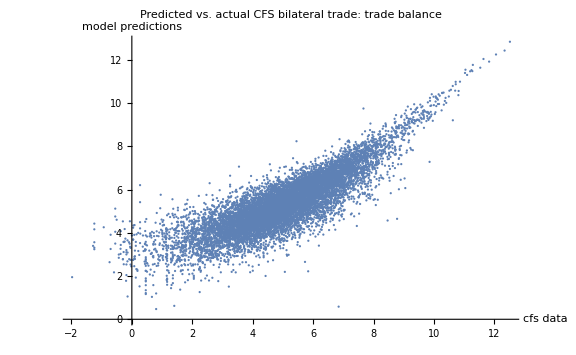

```mathematica
data=Log[Transpose[{Flatten[rescaledCfs],Flatten[cfsToCfsSales]}]];
data=DeleteCases[data,{_,Indeterminate}]; data=DeleteCases[data,{Indeterminate,_}];
ListPlot[data,PlotRange->All,AxesLabel->{"cfs data","model predictions"},ImageSize->Large,PlotLabel->"Predicted vs. actual CFS bilateral trade: trade balance"]
```

Comparing expenditure shares

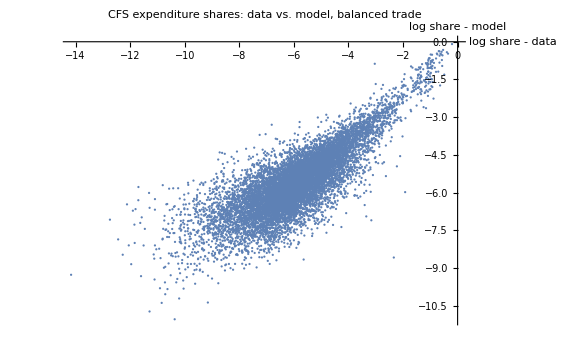

{10984,2}

```mathematica
cfsExpenditureShare=Transpose[Transpose[rescaledCfs]/Total[rescaledCfs]];
cfsToCfsSalesShare=Transpos e[Transpose[cfsToCfsSales]/Total[cfsToCfsSales]];

data=Log[Transpose[{Flatten[cfsExpenditureShare],Flatten[cfsToCfsSalesShare]}]];
data=DeleteCases[data,{_,Indeterminate}]; data=DeleteCases[data,{Indeterminate,_}];
ListPlot[data,PlotRange->All,ImageSize->Large,AxesLabel->{"log share - data","log share - model"},PlotLabel->"CFS expenditure shares: data vs. model, balanced trade"]
Dimensions[data]
(*the data is exported back to stata to produce figure B.2*)
Export["data\\comparisonCFS_shares_rescaled_fullTradeDeficits.csv", data];
```

Data for reduced form regressions

## Land prices

Exporting model-based land prices

```mathematica
landPrice=(1-α)resIncome/landArea;
landPriceDef=(1-α)(resIncome+deficit)/landArea;
varnames={{"land_price_nodeficit"},{"land_price_deficit"}};
out=Join[varnames,{landPrice,landPriceDef},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\land_prices_fullTD.csv", out]
```

data\land_prices_fullTD.csv

## Amenities inversion

This code computes amenity values that rationalize the observed commuting flows. They are used in generating data for footnote 25.

```mathematica
amenitiesBni=Block[{commcost,nlevel,ilevel,nilevel,bniguess,bninext,
dist,tol,c,num,den,rhs,gap,adj,mean,totflows,gapC,distC},

gapC=Compile[{{rr,_Real,2}},
Module[{gg},
gg=λ/(rr+isCommuting-1); 
gg
]
];
distC=Compile[{{gg,_Real,2}},
Module[{dd},
dd=Max[Abs[gg -1] isCommuting]; 
dd]
];

commcost=distancesAllPairs^(-ϕ ϵ);
Table[commcost[[i,i]]=1,{i,1,ncounties}];


nlevel=(workplaceEmp/Diagonal[πniOnlyTrading])^(-(α ϵ)/(σ-1))(prodOnlyTrading/workplaceWage)^(α ϵ)((resWage resEmp)/landArea)^(-ϵ (1-α)) ;
ilevel=workplaceWage^ϵ;
nilevel=commcost Outer[Times,nlevel,ilevel];
bniguess=λ/(Total[λ,2]/Total[isCommuting,2]); (*mean is one among those with positive commuting*)

dist=1;
tol=10^-6;
c=0;
adj=0.3;

totflows=Total[isCommutingSp,2];

While[dist>tol &&  c<100000,
c=c+1;

(*new set of numerators*)
num=bniguess nilevel;
den=Total[num,2];
rhs=num population/den;



gap=gapC[rhs];
dist=distC[gap];


bninext=gap bniguess;

mean=Total[bninext,2]/totflows;

bninext=bninext/mean;

bniguess=(1-adj) bniguess + adj bninext;




(*diagnostics*)
If[Mod[c,10]==0  && dist>0.0001,
Print["end of iteration ",c, " at " DateString[], "; max gap: ",dist,  " - ",Min[bniguess]," ",Max[bniguess]]
];

];

Print["end of iteration ",c, " at " DateString[], "; max gap: ",dist,  " - ",Min[bniguess]," ",Max[bniguess]];
Print["mean ",Total[bniguess,2]/Total[isCommuting,2]];
num=bniguess nilevel;
den=Total[num,2];
rhs=num population/den;

gap=gapC[rhs];
dist=distC[gap];

Print["dist: ",dist];

Print[λ[[1;;8,1;;8]]//MatrixForm];
Print[rhs[[1;;8,1;;8]]//MatrixForm];
Print[gap[[1;;8,1;;8]]//MatrixForm];



bniguess
];
```

end of iteration 10 at  Wed 22 Jan 2025 15:56:06; max gap: 8.27078×10^9 - 0. 6047.84

end of iteration 20 at  Wed 22 Jan 2025 15:56:09; max gap: 2.24371×10^8 - 0. 6218.63

end of iteration 30 at  Wed 22 Jan 2025 15:56:11; max gap: 6.33083×10^6 - 0. 6223.45

end of iteration 40 at  Wed 22 Jan 2025 15:56:13; max gap: 178825. - 0. 6223.59

end of iteration 50 at  Wed 22 Jan 2025 15:56:16; max gap: 5051.35 - 0. 6223.59

end of iteration 60 at  Wed 22 Jan 2025 15:56:18; max gap: 142.688 - 0. 6223.59

end of iteration 70 at  Wed 22 Jan 2025 15:56:21; max gap: 4.03059 - 0. 6223.59

end of iteration 80 at  Wed 22 Jan 2025 15:56:24; max gap: 0.998948 - 0. 6223.59

end of iteration 90 at  Wed 22 Jan 2025 15:56:26; max gap: 0.967502 - 0. 6223.59

end of iteration 100 at  Wed 22 Jan 2025 15:56:32; max gap: 0.457576 - 0. 6223.59

end of iteration 110 at  Wed 22 Jan 2025 15:56:36; max gap: 0.0232763 - 0. 6223.59

end of iteration 120 at  Wed 22 Jan 2025 15:56:42; max gap: 0.000672707 - 0. 6223.59

end of iteration 139 at  Wed 22 Jan 2025 15:56:51; max gap: 7.57912×10^-7 - 0. 6223.59

mean 1.

dist: 5.27711×10^-7

(13591.2 | 0 | 0 | 15.8029 | 0 | 0 | 14.7187 | 0
0 | 82518.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 10931.8 | 0 | 0 | 231.227 | 0 | 0
0 | 0 | 0 | 5215.09 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.3682 | 15685.9 | 0 | 0 | 74.5441
0 | 0 | 348.382 | 0 | 0 | 3086.86 | 0 | 0
11.3422 | 0 | 0 | 0 | 0 | 0 | 8649.76 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 51924.3)

(13591.2 | 0. | 0. | 15.8029 | 0. | 0. | 14.7187 | 0.
0. | 82518.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 10931.8 | 0. | 0. | 231.227 | 0. | 0.
0. | 0. | 0. | 5215.09 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2.3682 | 15685.9 | 0. | 0. | 74.5441
0. | 0. | 348.382 | 0. | 0. | 3086.86 | 0. | 0.
11.3422 | 0. | 0. | 0. | 0. | 0. | 8649.76 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 51924.3)

(1. | 0. | 0. | 1. | 0. | 0. | 1. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 1. | 0. | 0. | 1.
0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
Export["data\\amenitiesBni.csv", amenitiesBni];
```

## Statistics and partial derivatives

This section generates the “data_for_reduced_form_fullTD.csv” file in the data folder. This file contains partial derivatives for commuting, counties productivities and other statistics used in the stata file.

```mathematica
workIncome=(workplaceWage workplaceEmp)/10^6;
```

```mathematica
(*Exporting own elasticities*)
Block[{varnames,isIn120,emplAround,weights,workplaceWageAround,resAround,resWageAround,out,temp1,z1,z2,z3,z4,z5 ,αrn,μrn,λrnr},

isIn120=Table[If[distancesAllPairs[[i,j]]≤120,1,0],{i,1,ncounties},{j,1,ncounties}];
Table[isIn120[[i,i]]=0,{i,1,ncounties}];

emplAround=isIn120.workplaceEmp;
weights=Table[isIn120[[i,j]] workplaceEmp[[j]]/(emplAround[[i]]+isIn120[[i,j]]-1),{i,1,ncounties},{j,1,ncounties}] isIn120;
workplaceWageAround=weights.workplaceWage;
resAround=isIn120.resEmp;
weights=Table[isIn120[[i,j]] resEmp[[j]]/(resAround[[i]]+isIn120[[i,j]]-1),{i,1,ncounties},{j,1,ncounties}] isIn120;
resWageAround=weights.resWage;




αrn=Transpose[Transpose[πniOnlyTrading/laborIncome](resIncome+deficit)]; 
Print[{Min[Total[αrn,{2}]],Max[Total[αrn,{2}]]}];

μrn=1. Transpose[Transpose[λ]/workplaceEmp];
λrnr=1.0 λ/resEmp;

z1=Total[(1-λrnr) μrn];
z2=Diagonal[μrn](Diagonal[λ]/resEmp-workplaceEmp/Total[workplaceEmp]);
z3=Total[αrn (1-πniOnlyTrading),{2}]; (*for a fixed row producer/seller n, sum across all residences buying from it*)
z4=z1 z3;
z5=z2 z3;



varnames={{"workplaceemp"},{"resemp"},{"workplacewage"},{"resWage"},{"emplAround"},{"workplaceWageAround"},{"resAround"},{"resWageAround"},{"landArea"},{"lambda_nn_n"},{"pd_commuting"},{"pd_migration"},{"pd_goods"},{"pd_commuting_goods"},{"pd_migration_goods"},{"productivity"},{"deficit"}};
out=Join[varnames,{workplaceEmp,resEmp,workplaceWage,resWage,emplAround,workplaceWageAround,resAround,resWageAround,landArea,Diagonal[λrnr],z1,z2,z3,z4,z5,prodOnlyTrading,deficit},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\data_for_reduced_form_fullTD.csv", out] 
];
```

{0.999999,1.}

## Counterfactual Simulations

a) 5% shock to each county

This section generates the data for the main results in section 3, 5% productivity shock to each county, across all counties. The data is then imported in Stata for processing.

Set up of the simulations:

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
varnames={{"Repetition"},{"CountyLine"},{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"LambdaNNHat"},{"PiNNHat"},{"Ahat"},{"MeasuredProdHat"},{"ShipmentsHat"}};
(*setting number of replications: one shock per county*)
numberOfReplications=3111;
(*complete matrix of shocks: row number N has the shock profile for repetition N*)
prodShocks=1+DiagonalMatrix[Table[0.05,{i,1,numberOfReplications}]];
```

Computing outcomes

```mathematica
out2=Parallelize[
Table[countyProdShock[rep,prodShocks[[rep]],ηzero],{rep,1,numberOfReplications}]
];
```

CompiledFunction::cfta: Argument … at position 3 should be a rank 1 tensor of machine-size real numbers.

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\14.1\WolframKernel" -noicon -noinit -subkernel -wstp,4133,29].

KernelObject::rdead: Subkernel connected through KernelObject[«1»] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {180} assigned to KernelObject[«1»].

LaunchKernels::clone: Kernel KernelObject[«1»] resurrected as KernelObject[«1»].

CompiledFunction::cfta: Argument … at position 3 should be a rank 1 tensor of machine-size real numbers.

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\14.1\WolframKernel" -noicon -noinit -subkernel -wstp,4145,41].

KernelObject::rdead: Subkernel connected through KernelObject[«1»] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {192} assigned to KernelObject[«1»].

LaunchKernels::clone: Kernel KernelObject[«1»] resurrected as KernelObject[«1»].

CompiledFunction::cfta: Argument … at position 3 should be a rank 1 tensor of machine-size real numbers.

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Wolfram\14.1\WolframKernel" -noicon -noinit -subkernel -wstp,4138,34].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

KernelObject::rdead: Subkernel connected through KernelObject[«1»] appears dead.

General::stop: Further output of KernelObject::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {185} assigned to KernelObject[«1»].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[«1»] resurrected as KernelObject[«1»].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

CompiledFunction::cfta: Argument … at position 3 should be a rank 1 tensor of machine-size real numbers.

Exporting data in separate files

```mathematica
Print["Started on ",DateString[]];
Table[
Block[{repN,filename},
repN=ToString[rep];
If[rep<10,repN="000"<>repN];
If[rep≥10 && rep≤99,repN="00"<>repN];
If[rep≥100 && rep≤999,repN="0"<>repN];
filename="data\\county shocks 5pct\\county_oneShock5pct_rep"<>repN<>".csv";
Export[filename, out2[[rep,1]]];
],
{rep,1,numberOfReplications}];
Print["All export done on ",DateString[]];
```

Checking that all converged: max number of iteration is smaller than 2000, and distances from previous iteration smaller than 10^-6

```mathematica
{Max[Table[out2[[i,2]],{i,1,numberOfReplications}]],Max[Table[out2[[i,3]],{i,1,numberOfReplications}]],Max[Table[out2[[i,4]],{i,1,numberOfReplications}]]}
```

```mathematica
x`
```

b) 5% productivity shocks in a world without commuting

This section generates the data for figure C.7 in the appendix. The data is then imported in Stata for processing.

### A world with no commuting: generating initial values

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in productivity*)
dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
khat=Table[300,{i,1,ncounties},{j,1,ncounties}]-DiagonalMatrix[Table[299,{i,1,ncounties}]];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
el=Table[0,{i,1,ncounties}];
```

Computing changes from the initial equilibrium

```mathematica
nocomm=hatChanges[khat,dhat,ahat,bhat,el,2];
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=nocomm-1;
```

Checking welfare

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) ,{i,1,ncounties}];
{Min[wel],Max[wel]}
```

{0.927711,0.927711}

Computing new initial equilibrium

```mathematica
resEmpIn=resEmp (LRhatOut+1);
λIn=λ  (λhatOut+1);
workplaceEmpIn=workplaceEmp (LMhatOut+1);
resWageIn=resWage (VbarhatOut+1);
workplaceWageIn=workplaceWage (whatOut+1);
resIncomeIn=(resEmpIn resWageIn)/10^6;
workIncomeIn=(workplaceEmpIn workplaceWageIn)/10^6;
πniIn=πniOnlyTrading (πnihatOut+1);
```

Checking that all flows are the same and that in each location, residents and employment are identical in terms of wages and counts

```mathematica
Total[λ,2]/10^6
Total[λIn,2]/10^6
Max[Abs[(resEmpIn-workplaceEmpIn)/((resEmpIn+workplaceEmpIn) 0.5)]]
Max[Abs[(resWageIn-workplaceWageIn)/((resWageIn+workplaceWageIn) 0.5)]]
{Min[Total[πniIn]],Max[Total[πniIn]]}
```

### Productivity shocks in a world with no commuting

Set up of the simulations:

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
varnames={{"Repetition"},{"CountyLine"},{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"LambdaNNHat"},{"PiNNHat"},{"Ahat"},{"MeasuredProdHat"},{"ShipmentsHat"}};
(*setting number of replications: one shock per county*)
numberOfReplications=3111;
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
(*complete matrix of shocks: row number N has the shock profile for repetition N*)
prodShocks=1+DiagonalMatrix[Table[0.05,{i,1,numberOfReplications}]];
```

Computing outcomes

```mathematica
out2=Parallelize[
Table[countyProdShockArb[rep,khat, dhat,prodShocks[[rep]],bhat,λIn,workplaceWageIn,resWageIn,workplaceEmpIn,resEmpIn,πniIn,resIncomeIn,workIncomeIn, el],{rep,1,numberOfReplications}]
];
```

Exporting data in separate files

```mathematica
Print["Started on ",DateString[]];
Table[
Block[{repN,filename},
repN=ToString[rep];
If[rep<10,repN="000"<>repN];
If[rep≥10 && rep≤99,repN="00"<>repN];
If[rep≥100 && rep≤999,repN="0"<>repN];
filename="data\\county shocks 5 pct with no comm\\county_oneShock5pct_rep"<>repN<>".csv";
Export[filename, out2[[rep,1]]];
],
{rep,1,numberOfReplications}];
Print["All export done on ",DateString[]];
```

Checking that all converged: max number of iteration is smaller than 2000, and distances from previous iteration smaller than 10^-6

```mathematica
{Max[Table[out2[[i,2]],{i,1,numberOfReplications}]],Max[Table[out2[[i,3]],{i,1,numberOfReplications}]],Max[Table[out2[[i,4]],{i,1,numberOfReplications}]]}
```

c) Spatially correlated shocks

This exercise computes single-counterfactuals for three spatially correlated shocks (section C.4, figures C.4, C.5 and C.6 of the web appendix)

## Shock to Manufacturing only (productivity growth 2004-2010 from BLS)

This exercise generates data for figure C.4 of the web appendix.

```mathematica
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*total mfg tfp growth 2004-2010*)
tfpMfg=6.1199/100;
(*change in productivity*)
ahat=tfpMfg mfgShares+1;
(*counterfactual changes*)
spCorr=hatChangesA[ahat,ηzero, 25];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=spCorr-1;
Clear[c,distWages,distλ];

varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"},{"ownTrade"},{"mfgShare"},{"ahat"}};
ownCommHat=Diagonal[λhatOut];
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat,Diagonal[πniOnlyTrading],mfgShares,ahat},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\spatially correlated\\spCorr_mfg_BLS.csv",out];
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

## Shock to non-manufacturing only (productivity growth 2004-2010 from BLS)

This exercise generates data for figure C.5 of the web appendix.

```mathematica
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*total non-mfg tfp growth 2004-2010*)
tfpNonMfg=3.1177/100;
(*change in productivity*)
ahat=tfpNonMfg (1-mfgShares)+1;
(*counterfactual changes*)
spCorr=hatChangesA[ahat,ηzero, 25];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=spCorr-1;
Clear[c,distWages,distλ];
varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"},{"ownTrade"},{"mfgShare"},{"ahat"}};
ownCommHat=Diagonal[λhatOut];
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat,Diagonal[πniOnlyTrading],mfgShares,ahat},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\spatially correlated\\spCorr_nonMfg_BLS.csv",out];
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

## Shock to both sectors (productivity growth 2004-2010 from BLS)

This exercise generates data for figure C.6 of the web appendix.

```mathematica
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in productivity*)
tfpMfg=6.1199/100;
tfpNonMfg=3.1177/100;
ahat=tfpNonMfg (1-mfgShares)+mfgShares tfpMfg+1;
(*counterfactual changes*)
spCorr=hatChangesA[ahat,ηzero, 25];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=spCorr-1;
Clear[c,distWages,distλ];
varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"},{"ownTrade"},{"mfgShare"},{"ahat"}};
ownCommHat=Diagonal[λhatOut];
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat,Diagonal[πniOnlyTrading],mfgShares,ahat},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\spatially correlated\\spCorr_both_BLS.csv",out];
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

d) 5% shock to each county, positive land supply elasticity

This exercise computes counterfactuals using a positive land supply elasticity (figure 3, table C2).

Set up of the simulations:

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
varnames={{"Repetition"},{"CountyLine"},{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"LambdaNNHat"},{"PiNNHat"},{"Ahat"},{"MeasuredProdHat"},{"ShipmentsHat"}};
(*setting number of replications: one shock per county*)
numberOfReplications=3111;
```

```mathematica
(*complete matrix of shocks: row number N has the shock profile for repetition N*)
prodShocks=1+DiagonalMatrix[Table[0.05,{i,1,numberOfReplications}]];
```

Computing outcomes

```mathematica
out2=Parallelize[
Table[countyProdShock[rep,prodShocks[[rep]],ηexf],{rep,1,numberOfReplications}]
];
```

Exporting data in separate files

```mathematica
Print["Started on ",DateString[]];
Table[
Block[{repN,filename},
repN=ToString[rep];
If[rep<10,repN="000"<>repN];
If[rep≥10 && rep≤99,repN="00"<>repN];
If[rep≥100 && rep≤999,repN="0"<>repN];
filename="data\\Saiz price exf county shocks 5pct\\county_oneShock5pct_rep"<>repN<>".csv";
Export[filename, out2[[rep,1]]];
],
{rep,1,numberOfReplications}];
Print["All export done on ",DateString[]];
```

Checking that all converged: max number of iteration is smaller than 2000, and distances from previous iteration smaller than 10^-6

```mathematica
{Max[Table[out2[[i,2]],{i,1,numberOfReplications}]],Max[Table[out2[[i,3]],{i,1,numberOfReplications}]],Max[Table[out2[[i,4]],{i,1,numberOfReplications}]]}
```

e) Reducing commuting costs using HRI changes 1990-2007

## Reduction by the median change

We reduce commuting costs symmetrically for all counties. The reduction is the inverse of the median change in the HRI from 1990 to 2007. In this distribution, we only count counties with a positive HRI, and exclude residence=workplace cases (where HRI_hat=1). 
Note: to simulate the consequences of reducing commuting costs with a 50% higher or 50% lower ϵ (see footnote 42) it is sufficient to quit the Notebook (to clear all data), change the value of ϵ accordingly in the “Setup, Import Data >> Parameters”, and re-run.

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in commuting costs*)
comch=(.6601334)^(1/ϵ);
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
Table[khat[[i,i]]=1,{i,1,ncounties}];

dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
khat[[1;;4,1;;4]]//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

```mathematica
comm=hatChanges[khat,dhat,ahat,bhat,ηzero,25];
```

Iteration 1  concluded on Wed 22 Jan 2025 17:04:37; distWages is 9.17449×10^-7; distλ is 1.18057×10^-6.

Convergence achieved in 2 iterations on Wed 22 Jan 2025 17:04:41; distWages is 7.91126×10^-7; distλ is 4.6039×10^-7 ...

Counterfactuals completed on Wed 22 Jan 2025 17:04:43.

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=comm-1;
varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"},{"ownTrade"}};
```

```mathematica
ownCommHat=Diagonal[λhatOut];
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat,Diagonal[πniOnlyTrading]},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\decreaseMedian.csv",out];
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

{1.,1.}

## Increase by the median change

We increase commuting costs symmetrically for all counties. The increase is the median change in the HRI from 1990 to 2007. In this distribution, we only count counties with a positive HRI, and exclude residence=workplace cases (where HRI_hat=1).

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in commuting costs*)
comch=1.514845^(1/ϵ);
khat=Table[comch,{i,1,ncounties},{j,1,ncounties}];
Table[khat[[i,i]]=1,{i,1,ncounties}];

dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
khat[[1;;4,1;;4]]//MatrixForm
```

```mathematica
comm=hatChanges[khat,dhat,ahat,bhat,ηzero,25];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=comm-1;
```

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

{0.976652,0.976652}

## Reduction by the p25 change

We reduce commuting costs symmetrically for all counties. The reduction is the inverse of the p25 change in the HRI from 1990 to 2007. In this distribution, we only count counties with a positive HRI, and exclude residence=workplace cases (where HRI_hat=1).

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in commuting costs*)
comch=(.8805599)^(1/ϵ);
khat=Table[comch,{i,1,ncounties},{j,1,ncounties}];
Table[khat[[i,i]]=1,{i,1,ncounties}];

dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
khat[[1;;4,1;;4]]//MatrixForm
```

```mathematica
comm=hatChanges[khat,dhat,ahat,bhat,ηzero,25];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=comm-1;
```

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

{1.0089,1.0089}

## Reduction by the p75 change

We reduce commuting costs symmetrically for all counties. The reduction is the inverse of the p75 change in the HRI from 1990 to 2007. In this distribution, we only count counties with a positive HRI, and exclude residence=workplace cases (where HRI_hat=1).

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in commuting costs*)
comch=(.4664594)^(1/ϵ);
khat=Table[comch,{i,1,ncounties},{j,1,ncounties}];
Table[khat[[i,i]]=1,{i,1,ncounties}];

dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

```mathematica
khat[[1;;4,1;;4]]//MatrixForm
```

```mathematica
comm=hatChanges[khat,dhat,ahat,bhat,ηzero,25];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=comm-1;
```

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) bhat[[i,i]]^(1/ϵ),{i,1,ncounties}];
{Min[wel],Max[wel]}
```

{1.06888,1.06888}

f) Reducing trade costs in worlds with and without commuting

## Changing trade costs in the current world

In this exercise we compute the effect of reducing trade costs by 20% in the initial equilibrium.

### Reducing trade costs 20% from the initial equilibrium

```mathematica
(*change in distances; already exponentiated*)
dhat=Table[0.8,{i,1,ncounties},{j,1,ncounties}]-DiagonalMatrix[Table[-0.2,{i,1,ncounties}]];
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
```

```mathematica
lowTradeInitialEq=hatChanges[khat,dhat,ahat,bhat,ηzero,25];
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=lowTradeInitialEq-1;
```

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) ,{i,1,ncounties}];
{Min[wel],Max[wel]}
```

```mathematica
varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"}};
ownCommHat=(Diagonal[λhatOut]+1)/(LRhatOut+1)-1;
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\TradeLess20InitialEq.csv",out];
```

```mathematica
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=lowTradeInitialEq-1;
```

## Changing trade costs in a world with no commuting

In this exercise we compute the effect of reducing trade costs by 20% starting from a counterfactual world where commuting is not allowed.

### A world with no commuting: generating initial values

```mathematica
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
(*change in productivity*)
dhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
khat=Table[100,{i,1,ncounties},{j,1,ncounties}]-DiagonalMatrix[Table[99,{i,1,ncounties}]];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
```

Computing changes from the initial equilibrium

```mathematica
nocomm=hatChanges[khat,dhat,ahat,bhat,ηzero,25];
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=nocomm-1;
```

Checking welfare

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) ,{i,1,ncounties}];
{Min[wel],Max[wel]}
```

Computing new initial equilibrium

```mathematica
resEmpIn=resEmp (LRhatOut+1);
λIn=λ  (λhatOut+1);
workplaceEmpIn=workplaceEmp (LMhatOut+1);
resWageIn=resWage (VbarhatOut+1);
workplaceWageIn=workplaceWage (whatOut+1);
resIncomeIn=(resEmpIn resWageIn)/10^6;
workIncomeIn=(workplaceEmpIn workplaceWageIn)/10^6;
πniIn=πniOnlyTrading (πnihatOut+1);
```

Checking total population

```mathematica
Total[λ,2]/10^6
Total[λIn,2]/10^6
Max[Abs[(resEmpIn-workplaceEmpIn)/((resEmpIn+workplaceEmpIn) 0.5)]]
Max[Abs[(resWageIn-workplaceWageIn)/((resWageIn+workplaceWageIn) 0.5)]]
{Min[Total[πniIn]],Max[Total[πniIn]]}
```

### Reducing trade costs 20% in the world with no commuting

```mathematica
(*change in distances; already exponentiated*)
dhat=Table[0.8,{i,1,ncounties},{j,1,ncounties}]-DiagonalMatrix[Table[-0.2,{i,1,ncounties}]];
khat=Table[1,{i,1,ncounties},{j,1,ncounties}];
ahat=Table[1,{i,1,ncounties}];
bhat=Table[1,{i,1,ncounties},{j,1,ncounties}];
(*tolerance, max number of iterations, speed of adjustment*)
tol=10^-6; maxiter=1000; ζ=0.7;
```

```mathematica
lowTradeNoComm=hatChangesArb[khat,dhat,ahat,bhat,λIn,workplaceWageIn,resWageIn,workplaceEmpIn,resEmpIn,πniIn,resIncomeIn,workIncomeIn,ηzero,25];
{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,λhatOut,πnihatOut,c,distWages,distλ}=lowTradeNoComm-1;
```

```mathematica
wel=Table[(whatOut[[i]]+1)/(khat[[i,i]] (λhatOut[[i,i]]+1)^(1/ϵ) (PhatOut[[i]]+1)^α(QhatOut[[i]]+1)^(1-α)) ,{i,1,ncounties}];
{Min[wel],Max[wel]}
```

```mathematica
varnames={{"WHat"},{"VbarHat"},{"RealIncHat"},{"LMhat"},{"LRhat"},{"QHat"},{"PHat"},{"PriceHat"},{"OwnCommutingHat"},{"OwnTradeHat"}};
ownCommHat=(Diagonal[λhatOut]+1)/(LRhatOut+1)-1;
ownTradeHat=Diagonal[πnihatOut];
out=Join[varnames,{whatOut,VbarhatOut,realinchatOut,LMhatOut,LRhatOut,QhatOut,PhatOut,pricehatOut,ownCommHat,ownTradeHat},2];
out=Transpose[out];
out=Join[countyNames,out,2];
Export["data\\TradeLess20Nocomm.csv",out];
```